```mathematica
Needs["PhysicalConstants`"]
```

```mathematica
(* Introduce parameters *)

Z=83;
α=0.0072973525376;
e=ElectronCharge/Coulomb;
element=-Z;
diracPointEnergy [Ze_,n_,k_]:=(Export["imputdata2.dat",{{Ze,n,k}}];SetPrecision[RunThrough["c:\\f\\radial\\pointdiracwaves",Ze],13]);
 En[Ze_,n_,k_]:=α^-2 (1+(α*Ze)^2/(((k^2-(α Ze)^2)^(1/2)+n-Abs[k])^2))^(-1/2);
```

```mathematica
BPolynomial[n_,i_,a_,b_,x_]:=Binomial[n,i]((x-a)^i (b-x)^(n-i))/(b-a)^n
```

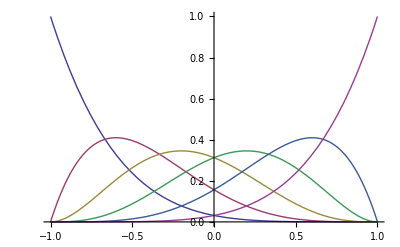

```mathematica
Plot[Evaluate[Table[BPolynomial[5,k,-1,1,x],{k,0,5}]],{x,-1,1}]
```

```mathematica
cMat[n_,i_,j_,R_]:=∫_0^R BPolynomial[n,i,0,R,x] BPolynomial[n,j,0,R,x]ⅆx
```

```mathematica
cMat[2,0,0,1]
```

1/5

```mathematica
dMat[n_,i_,j_,R_]:=∫_0^R BPolynomial[n,i,0,R,x] D[BPolynomial[n,j,0,R,x], x]ⅆx
```

```mathematica
dMat[2,0,0,1]
```

-1/2

```mathematica
kappaMat[n_,i_,j_,R_,k_]:=NIntegrate[BPolynomial[n,i,0,R,x] (k/x) BPolynomial[n,j,0,R,x],{x,0,R},Method->{"GlobalAdaptive","SingularityDepth"->20,"SingularityHandler"->{"IMT","TuningParameters"->{10,2}}},MaxRecursion->15,WorkingPrecision->MachinePrecision];
```

```mathematica
cMat[n_,R_]:=Table[cMat[n,i,j,R],{i,0,n},{j,0,n}]
```

```mathematica
cMat[2,1]
```

{{1/5,1/10,1/30},{1/10,2/15,1/10},{1/30,1/10,1/5}}

```mathematica
dMat[n_,R_]:=Table[dMat[n,i,j,R],{i,0,n},{j,0,n}]
```

```mathematica
MatrixForm[cMat[2,1]]
```

(1/5 | 1/10 | 1/30
1/10 | 2/15 | 1/10
1/30 | 1/10 | 1/5)

```mathematica
vMat[n_,i_,j_,R_]:=NIntegrate[BPolynomial[n,i,0,R,x] ((-Z e^2)/x) BPolynomial[n,j,0,R,x],{x,0,R},Exclusions->{0}];
```

```mathematica
kappaMat[n_,R_,k_]:=Table[kappaMat[n,i,j,R,k],{i,0,n},{j,0,n}]
```

```mathematica
vMat[n_,R_]:=Table[vMat[n,i,j,R],{i,0,n},{j,0,n}]
```

```mathematica
ϵMat[n_,elem_,nprime_,k_]:=En [elem,nprime,k] IdentityMatrix[n+1];
```

```mathematica
MatrixForm[ϵMat[2,element,2,-1]]
```

(17793.9 | 0. | 0.
0. | 17793.9 | 0.
0. | 0. | 17793.9)

```mathematica
MatrixForm[kappaMat[1,1,-1]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in x near {x} = {0.0000302747}. NIntegrate obtained -15.3033 and 1.83941 for the integral and error estimates.

(-15.3033 | -0.5
-0.5 | -0.5)

```mathematica
kappaMat1[n_,i_,j_,R_,k_]:=Integrate[BPolynomial[n,i,0,R,x] (k/x) BPolynomial[n,j,0,R,x],x]
```

```mathematica
kappaMat1[2,0,0,R,k]
```

(k ((25 R^4)/12-4 R^3 x+3 R^2 x^2-(4 R x^3)/3+x^4/4+R^4 Log[-x]))/R^4

```mathematica
%/.x->-r
```

(k (r^4/4+(4 r^3 R)/3+3 r^2 R^2+4 r R^3+(25 R^4)/12+R^4 Log[r]))/R^4

```mathematica
%%/.x->-ϵ
```

(k ((25 R^4)/12+4 R^3 ϵ+3 R^2 ϵ^2+(4 R ϵ^3)/3+ϵ^4/4+R^4 Log[ϵ]))/R^4

```mathematica
%%%/.x->R
```

k Log[-R]

```mathematica
%%%%/.x->r
```

(k (r^4/4-(4 r^3 R)/3+3 r^2 R^2-4 r R^3+(25 R^4)/12+R^4 Log[-r]))/R^4

```mathematica
((k (r^4/4+(4 r^3 R)/3+3 r^2 R^2+4 r R^3+(25 R^4)/12+R^4 Log[r]))/R^4)-((k ((25 R^4)/12+4 R^3 ϵ+3 R^2 ϵ^2+(4 R ϵ^3)/3+ϵ^4/4+R^4 Log[ϵ]))/R^4)+(k Log[-R])-((k (r^4/4-(4 r^3 R)/3+3 r^2 R^2-4 r R^3+(25 R^4)/12+R^4 Log[-r]))/R^4)
```

-(k (r^4/4-(4 r^3 R)/3+3 r^2 R^2-4 r R^3+(25 R^4)/12+R^4 Log[-r]))/R^4+(k (r^4/4+(4 r^3 R)/3+3 r^2 R^2+4 r R^3+(25 R^4)/12+R^4 Log[r]))/R^4+k Log[-R]-(k ((25 R^4)/12+4 R^3 ϵ+3 R^2 ϵ^2+(4 R ϵ^3)/3+ϵ^4/4+R^4 Log[ϵ]))/R^4

```mathematica
Simplify[%]
```

1/12 k (-25+(32 r^3)/R^3+(96 r)/R-(48 ϵ)/R-(36 ϵ^2)/R^2-(16 ϵ^3)/R^3-(3 ϵ^4)/R^4-12 Log[-r]+12 Log[r]+12 Log[-R]-12 Log[ϵ])

```mathematica
FullSimplify[%%]
```

(k (32 r^3 R+96 r R^3-(R+ϵ) (25 R^3+23 R^2 ϵ+13 R ϵ^2+3 ϵ^3)+12 R^4 (-Log[-r]+Log[r]+Log[-R]-Log[ϵ])))/(12 R^4)